# Dynamic Nuclear Polarization

```mathematica
Sz=1/2{{1,0},{0,-1}};
Sx=1/2{{0,1},{1,0}};
Sy=1/2{{0,-ⅈ},{ⅈ,0}};
Iz=1/2{{1,0},{0,-1}};
Ix=1/2{{0,1},{1,0}};
Iy=1/2{{0,-ⅈ},{ⅈ,0}};
II={{1,0},{0,1}};
sp[1]={1,0};
sp[2]={0,1};
```

## Some constants

```mathematica
e = 1.602176487 10^-19 C;
ℏ=1.054571628 10^-34(*J s*);
c=299792458 m s^-1;
me=9.10938215 10^-31 kg;
mp=1.672621637 10^-27 kg;
gp=5.585694713;
ge=-2.00231904622;
μ0=4 π 10^-7 kg/(m s^2);
ϵ0= 1/(μ0 c^2)//N;
α=e^2/((4π ϵ0)ℏ c);
a=ℏ/(me c α);
```

```mathematica
μe=-ge (e ℏ)/(2me)kg/C
μp=gp (e ℏ)/(2 mp) kg/C
γe=μe/(2π ℏ) (* in Hz *)
γp=μp/(2π ℏ)(* in Hz *)
```

1.85695×10^-23

2.82121×10^-26

2.8025×10^10

4.25775×10^7

## Solid effect

```mathematica
Solid effect only invole 1 electron and 1 nuclear spin.
```

```mathematica
(* The Hyperfine coupling is *)
HF=A S.II
```

```mathematica
(* the hyperfine coupling constant *)
A=μ0/(4π)8 π/3 μe μp 1/(π a^3)  s^14/(C^6 kg^7 m^2)
f=A/(2π ℏ)
λ=c/f
```

9.42762×10^-25

1.42281×10^9

(0.210705 m)/s

```mathematica
(*expectation of operator Q by v state*)
ExpV[u_,Q_,v_]:=u.Q.v
Hfgen[us_,ui_,vs_,vi_]:=A (
ExpV[us,Sx,vs]ExpV[ui,Ix,vi]+
ExpV[us,Sy,vs]ExpV[ui,Iy,vi]+
ExpV[us,Sz,vs]ExpV[ui,Iz,vi])
Hf={{Hfgen[sp[1],sp[1],sp[1],sp[1]],Hfgen[sp[1],sp[1],sp[1],sp[2]],Hfgen[sp[1],sp[1],sp[2],sp[1]],Hfgen[sp[1],sp[1],sp[2],sp[2]]},
{Hfgen[sp[1],sp[2],sp[1],sp[1]],Hfgen[sp[1],sp[2],sp[1],sp[2]],Hfgen[sp[1],sp[2],sp[2],sp[1]],Hfgen[sp[1],sp[2],sp[2],sp[2]]},
{Hfgen[sp[2],sp[1],sp[1],sp[1]],Hfgen[sp[2],sp[1],sp[1],sp[2]],Hfgen[sp[2],sp[1],sp[2],sp[1]],Hfgen[sp[2],sp[1],sp[2],sp[2]]},
{Hfgen[sp[2],sp[2],sp[1],sp[1]],Hfgen[sp[2],sp[2],sp[1],sp[2]],Hfgen[sp[2],sp[2],sp[2],sp[1]],Hfgen[sp[2],sp[2],sp[2],sp[2]]}};
```

```mathematica
Hf//MatrixForm
```

(A/4 | 0 | 0 | 0
0 | -A/4 | A/2 | 0
0 | A/2 | -A/4 | 0
0 | 0 | 0 | A/4)

```mathematica
Eigensystem[Hf]
```

{{-(3 A)/4,A/4,A/4,A/4},{{0,-1,1,0},{0,0,0,1},{0,1,1,0},{1,0,0,0}}}

```mathematica
(* population *)
ρ0={{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}};
ρ=MatrixExp[ⅈ/ℏ Hf t].ρ0.MatrixExp[-ⅈ Hf/ℏ t]//ExpToTrig//Simplify
```

```mathematica
(* Zeeman effect *)
Hz=-μe Bz Sz-μp Bz Sz
```

```mathematica
Hzgen[us_,ui_,vs_,vi_]:=-μe Bz ExpV[us,Sz,vs]ExpV[ui,II,vi]- μp Bz ExpV[us,II,vs] ExpV[ui,Iz,vi]
Hz={{Hzgen[sp[1],sp[1],sp[1],sp[1]],Hzgen[sp[1],sp[1],sp[1],sp[2]],Hzgen[sp[1],sp[1],sp[2],sp[1]],Hzgen[sp[1],sp[1],sp[2],sp[2]]},
{Hzgen[sp[1],sp[2],sp[1],sp[1]],Hzgen[sp[1],sp[2],sp[1],sp[2]],Hzgen[sp[1],sp[2],sp[2],sp[1]],Hzgen[sp[1],sp[2],sp[2],sp[2]]},
{Hzgen[sp[2],sp[1],sp[1],sp[1]],Hzgen[sp[2],sp[1],sp[1],sp[2]],Hzgen[sp[2],sp[1],sp[2],sp[1]],Hzgen[sp[2],sp[1],sp[2],sp[2]]},
{Hzgen[sp[2],sp[2],sp[1],sp[1]],Hzgen[sp[2],sp[2],sp[1],sp[2]],Hzgen[sp[2],sp[2],sp[2],sp[1]],Hzgen[sp[2],sp[2],sp[2],sp[2]]}};
```

```mathematica
Hf+Hz//MatrixForm
```

(A/4-(Bz μe)/2-(Bz μp)/2 | 0 | 0 | 0
0 | -A/4-(Bz μe)/2+(Bz μp)/2 | A/2 | 0
0 | A/2 | -A/4+(Bz μe)/2-(Bz μp)/2 | 0
0 | 0 | 0 | A/4+(Bz μe)/2+(Bz μp)/2)

```mathematica
Eigensystem[(Hf+Hz)]//FullSimplify
```

{{1/4 (A-2 Bz (μe+μp)),1/4 (A+2 Bz (μe+μp)),1/4 (-A-2 √(A^2+Bz^2 (μe-μp)^2)),1/4 (-A+2 √(A^2+Bz^2 (μe-μp)^2))},{{1,0,0,0},{0,0,0,1},{0,(-√(A^2+Bz^2 (μe-μp)^2)+Bz (-μe+μp))/A,1,0},{0,(√(A^2+Bz^2 (μe-μp)^2)+Bz (-μe+μp))/A,1,0}}}

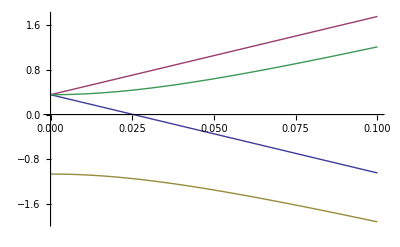

```mathematica
Plot[{1/4 (A-2 Bz (μe+μp))1/(2π 10^9 ℏ),1/4 (A+2 Bz (μe+μp))1/(2π 10^9 ℏ),1/4 (-A-2 √(A^2+Bz^2 (μe-μp)^2))1/(2π 10^9 ℏ),1/4 (-A+2 √(A^2+Bz^2 (μe-μp)^2))1/(2π 10^9 ℏ)},{Bz,0,0.1}](* in GHz *)
```

```mathematica
(* population *)
ρ0={{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}};
ρ=MatrixExp[ⅈ/ℏ(Hf+Hz) t].ρ0.MatrixExp[-ⅈ/ℏ(Hf+Hz) t]//ExpToTrig//Expand//Simplify;
ComplexExpand[ρ//MatrixForm]
```

(0 | 0 | 0 | 0
0 | (A^2+2 Bz^2 (μe-μp)^2+A^2 Cosh[(t √(-A^2-Bz^2 (μe-μp)^2))/ℏ])/(2 (A^2+Bz^2 (μe-μp)^2)) | (A Sinh[(t √(-A^2-Bz^2 (μe-μp)^2))/(2 ℏ)] (ⅈ (A^2+Bz^2 (μe-μp)^2) Cosh[(t √(-A^2-Bz^2 (μe-μp)^2))/(2 ℏ)]-Bz √(-A^2-Bz^2 (μe-μp)^2) (μe-μp) Sinh[(t √(-A^2-Bz^2 (μe-μp)^2))/(2 ℏ)]))/((-A^2-Bz^2 (μe-μp)^2)^(3/2)) | 0
0 | (A Sinh[(t √(-A^2-Bz^2 (μe-μp)^2))/(2 ℏ)] (-ⅈ (A^2+Bz^2 (μe-μp)^2) Cosh[(t √(-A^2-Bz^2 (μe-μp)^2))/(2 ℏ)]-Bz √(-A^2-Bz^2 (μe-μp)^2) (μe-μp) Sinh[(t √(-A^2-Bz^2 (μe-μp)^2))/(2 ℏ)]))/((-A^2-Bz^2 (μe-μp)^2)^(3/2)) | -(A^2 Sinh[(t √(-A^2-Bz^2 (μe-μp)^2))/(2 ℏ)]^2)/(A^2+Bz^2 (μe-μp)^2) | 0
0 | 0 | 0 | 0)

```mathematica
Manipulate[Plot[{(A^2+2 Bz^2 (μe-μp)^2+A^2 Cos[(t √(A^2+Bz^2 (μe-μp)^2))/ℏ])/(2 (A^2+Bz^2 (μe-μp)^2)),(A^2 Sin[1/2 t/ℏ √(A^2+Bz^2 (μe-μp)^2)]^2)/(A^2+Bz^2 (μe-μp)^2),((A^2+2 Bz^2 (μe-μp)^2+A^2 Cos[t/ℏ √(A^2+Bz^2 (μe-μp)^2)])/(2 (A^2+Bz^2 (μe-μp)^2))-(A^2 Sin[1/2 t/ℏ √(A^2+Bz^2 (μe-μp)^2)]^2)/(A^2+Bz^2 (μe-μp)^2))}
,{t,0,10^-9},PlotLabel->"Electron and Proton polarization"]
,{{Bz,0,"external Magnetic field"},0,1}

]
```

```mathematica
(* Rotation Operator *)
Uz[θ_]:=MatrixExp[-ⅈ θ Sz]
Uz[θ]
```

{{ⅇ^(-(ⅈ θ)/2),0},{0,ⅇ^((ⅈ θ)/2)}}

```mathematica
(* microwave *)
Hw= -μe Bx Uz[-ω t].Sx.Uz[ω t]-μp Bx Uz[-ω t].Ix.Uz[ω t]
```

{{0.,-9.29887×10^-24 Bx ⅇ^(ⅈ t ω)},{-9.29887×10^-24 Bx ⅇ^(-ⅈ t ω),0.}}

```mathematica
Hwgen[us_,ui_,vs_,vi_]:=-μe Bx ExpV[us,Uz[-ω t].Sx.Uz[ω t],vs]ExpV[ui,II,vi]- μp Bx ExpV[us,II,vs] ExpV[ui,Uz[-ω t].Ix.Uz[ω t],vi]
Hw={{Hwgen[sp[1],sp[1],sp[1],sp[1]],Hwgen[sp[1],sp[1],sp[1],sp[2]],Hwgen[sp[1],sp[1],sp[2],sp[1]],Hwgen[sp[1],sp[1],sp[2],sp[2]]},
{Hwgen[sp[1],sp[2],sp[1],sp[1]],Hwgen[sp[1],sp[2],sp[1],sp[2]],Hwgen[sp[1],sp[2],sp[2],sp[1]],Hwgen[sp[1],sp[2],sp[2],sp[2]]},
{Hwgen[sp[2],sp[1],sp[1],sp[1]],Hwgen[sp[2],sp[1],sp[1],sp[2]],Hwgen[sp[2],sp[1],sp[2],sp[1]],Hwgen[sp[2],sp[1],sp[2],sp[2]]},
{Hwgen[sp[2],sp[2],sp[1],sp[1]],Hwgen[sp[2],sp[2],sp[1],sp[2]],Hwgen[sp[2],sp[2],sp[2],sp[1]],Hwgen[sp[2],sp[2],sp[2],sp[2]]}};
```

```mathematica
Hw//MatrixForm
```

(0 | -1/2 Bx ⅇ^(ⅈ t ω) μp | -1/2 Bx ⅇ^(ⅈ t ω) μe | 0
-1/2 Bx ⅇ^(-ⅈ t ω) μp | 0 | 0 | -1/2 Bx ⅇ^(ⅈ t ω) μe
-1/2 Bx ⅇ^(-ⅈ t ω) μe | 0 | 0 | -1/2 Bx ⅇ^(ⅈ t ω) μp
0 | -1/2 Bx ⅇ^(-ⅈ t ω) μe | -1/2 Bx ⅇ^(-ⅈ t ω) μp | 0)

```mathematica
Hf+Hz+Hw//MatrixForm
```

(A/4-(Bz μe)/2-(Bz μp)/2 | -1/2 Bx ⅇ^(ⅈ t ω) μp | -1/2 Bx ⅇ^(ⅈ t ω) μe | 0
-1/2 Bx ⅇ^(-ⅈ t ω) μp | -A/4-(Bz μe)/2+(Bz μp)/2 | A/2 | -1/2 Bx ⅇ^(ⅈ t ω) μe
-1/2 Bx ⅇ^(-ⅈ t ω) μe | A/2 | -A/4+(Bz μe)/2-(Bz μp)/2 | -1/2 Bx ⅇ^(ⅈ t ω) μp
0 | -1/2 Bx ⅇ^(-ⅈ t ω) μe | -1/2 Bx ⅇ^(-ⅈ t ω) μp | A/4+(Bz μe)/2+(Bz μp)/2)

```mathematica
Eigensystem[Hf+Hz+Hw]//FullSimplify
```

{{1/4 (A-2 √((Bx^2+Bz^2) (μe+μp)^2)),1/4 (A+2 √((Bx^2+Bz^2) (μe+μp)^2)),1/4 (-A-2 √(A^2+(Bx^2+Bz^2) (μe-μp)^2)),1/4 (-A+2 √(A^2+(Bx^2+Bz^2) (μe-μp)^2))},{{(ⅇ^(2 ⅈ t ω) (Bx^2 (μe+μp)+2 Bz (Bz (μe+μp)+√((Bx^2+Bz^2) (μe+μp)^2))))/(Bx^2 (μe+μp)),(ⅇ^(ⅈ t ω) (Bz (μe+μp)+√((Bx^2+Bz^2) (μe+μp)^2)))/(Bx (μe+μp)),(ⅇ^(ⅈ t ω) (Bz (μe+μp)+√((Bx^2+Bz^2) (μe+μp)^2)))/(Bx (μe+μp)),1},{(ⅇ^(2 ⅈ t ω) ((Bx^2+2 Bz^2) (μe+μp)-2 Bz √((Bx^2+Bz^2) (μe+μp)^2)))/(Bx^2 (μe+μp)),(ⅇ^(ⅈ t ω) (Bz (μe+μp)-√((Bx^2+Bz^2) (μe+μp)^2)))/(Bx (μe+μp)),(ⅇ^(ⅈ t ω) (Bz (μe+μp)-√((Bx^2+Bz^2) (μe+μp)^2)))/(Bx (μe+μp)),1},{-ⅇ^(2 ⅈ t ω),(ⅇ^(ⅈ t ω) (A+√(A^2+(Bx^2+Bz^2) (μe-μp)^2)+Bz (μe-μp)))/(Bx (μe-μp)),-(ⅇ^(ⅈ t ω) (A+√(A^2+(Bx^2+Bz^2) (μe-μp)^2)+Bz (-μe+μp)))/(Bx (μe-μp)),1},{-ⅇ^(2 ⅈ t ω),(ⅇ^(ⅈ t ω) (A-√(A^2+(Bx^2+Bz^2) (μe-μp)^2)+Bz (μe-μp)))/(Bx (μe-μp)),(ⅇ^(ⅈ t ω) (-A+√(A^2+(Bx^2+Bz^2) (μe-μp)^2)+Bz (μe-μp)))/(Bx (μe-μp)),1}}}

```mathematica
Manipulate[Plot[{1/4 (A-2 √((Bx^2+Bz^2) (μe+μp)^2))1/(2π 10^9 ℏ),1/4 (A+2 √((Bx^2+Bz^2) (μe+μp)^2))1/(2π 10^9 ℏ),1/4 (-A-2 √(A^2+(Bx^2+Bz^2) (μe-μp)^2))1/(2π 10^9 ℏ),1/4 (-A+2 √(A^2+(Bx^2+Bz^2) (μe-μp)^2))1/(2π 10^9 ℏ)},{Bz,0,0.1}],{Bx,0,1}](* in GHz*)
```

```mathematica
(* population *)
ρ0={{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}};
ρ=MatrixExp[ⅈ/ℏ(Hf+Hz+Hw) t].ρ0.MatrixExp[-ⅈ/ℏ (Hf+Hz+Hw) t]//FullSimplify;
ρ[[2]][[2]]
```

RootSum[(-7.48489×10^37+0. ⅈ) ⅇ^(4 ⅈ t ω)+(7.79083×10^40+0. ⅈ) Bx^2 ⅇ^(4 ⅈ t ω)+(6.00865×10^43+0. ⅈ) Bx^4 ⅇ^(4 ⅈ t ω)+(6.1897×10^26+0. ⅈ) Bx^2 Bz ⅇ^(4 ⅈ t ω)+(7.79083×10^40+0. ⅈ) Bz^2 ⅇ^(4 ⅈ t ω)+(1.20173×10^44+0. ⅈ) Bx^2 Bz^2 ⅇ^(4 ⅈ t ω)+(6.00865×10^43+0. ⅈ) Bz^4 ⅇ^(4 ⅈ t ω)-(0.+8.93075×10^28 ⅈ) ⅇ^(3 ⅈ t ω) #1+(0.+2.10562×10^29 ⅈ) Bx^2 ⅇ^(3 ⅈ t ω) #1-(0.+8.19092×10^16 ⅈ) Bx^2 Bz ⅇ^(3 ⅈ t ω) #1+(0.+2.10562×10^29 ⅈ) Bz^2 ⅇ^(3 ⅈ t ω) #1+(2.99698×10^19+0. ⅈ) ⅇ^(2 ⅈ t ω) #1^2+(1.55032×10^22+0. ⅈ) Bx^2 ⅇ^(2 ⅈ t ω) #1^2+(1.55032×10^22+0. ⅈ) Bz^2 ⅇ^(2 ⅈ t ω) #1^2-(0.+0.0000152588 ⅈ) Bz ⅇ^(ⅈ t ω) #1^3+1. #1^4&,((0.-1.11634×10^28 ⅈ) ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)-(0.+1.73243×10^31 ⅈ) Bx^2 ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)+(0.+4.39103×10^29 ⅈ) Bz ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)-(0.+6.83506×10^32 ⅈ) Bx^2 Bz ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)+(0.+1.7377×10^31 ⅈ) Bz^2 ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)-(0.+6.83506×10^32 ⅈ) Bz^3 ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)+(4.99496×10^18+0. ⅈ) ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1+(7.75158×10^21+0. ⅈ) Bx^2 ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1-(3.92944×10^20+0. ⅈ) Bz ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1+(7.77514×10^21+0. ⅈ) Bz^2 ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1-(0.+2.23494×10^9 ⅈ) ⅇ^(ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1^2-(0.+8.79092×10^10 ⅈ) Bz ⅇ^(ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1^2+ⅇ^(1. ⅇ^(-ⅈ t ω) t #1) #1^3)/((0.-8.93075×10^28 ⅈ) ⅇ^(3 ⅈ t ω)+(0.+2.10562×10^29 ⅈ) Bx^2 ⅇ^(3 ⅈ t ω)-(0.+8.19092×10^16 ⅈ) Bx^2 Bz ⅇ^(3 ⅈ t ω)+(0.+2.10562×10^29 ⅈ) Bz^2 ⅇ^(3 ⅈ t ω)+(5.99395×10^19+0. ⅈ) ⅇ^(2 ⅈ t ω) #1+(3.10063×10^22+0. ⅈ) Bx^2 ⅇ^(2 ⅈ t ω) #1+(3.10063×10^22+0. ⅈ) Bz^2 ⅇ^(2 ⅈ t ω) #1-(0.+0.0000457764 ⅈ) Bz ⅇ^(ⅈ t ω) #1^2+4. #1^3)&] RootSum[(-7.48489×10^37+0. ⅈ) ⅇ^(4 ⅈ t ω)+(7.79083×10^40+0. ⅈ) Bx^2 ⅇ^(4 ⅈ t ω)+(6.00865×10^43+0. ⅈ) Bx^4 ⅇ^(4 ⅈ t ω)+(6.1897×10^26+0. ⅈ) Bx^2 Bz ⅇ^(4 ⅈ t ω)+(7.79083×10^40+0. ⅈ) Bz^2 ⅇ^(4 ⅈ t ω)+(1.20173×10^44+0. ⅈ) Bx^2 Bz^2 ⅇ^(4 ⅈ t ω)+(6.00865×10^43+0. ⅈ) Bz^4 ⅇ^(4 ⅈ t ω)+(0.+8.93075×10^28 ⅈ) ⅇ^(3 ⅈ t ω) #1-(0.+2.10562×10^29 ⅈ) Bx^2 ⅇ^(3 ⅈ t ω) #1+(0.+8.19092×10^16 ⅈ) Bx^2 Bz ⅇ^(3 ⅈ t ω) #1-(0.+2.10562×10^29 ⅈ) Bz^2 ⅇ^(3 ⅈ t ω) #1+(2.99698×10^19+0. ⅈ) ⅇ^(2 ⅈ t ω) #1^2+(1.55032×10^22+0. ⅈ) Bx^2 ⅇ^(2 ⅈ t ω) #1^2+(1.55032×10^22+0. ⅈ) Bz^2 ⅇ^(2 ⅈ t ω) #1^2+(0.+0.0000152588 ⅈ) Bz ⅇ^(ⅈ t ω) #1^3+1. #1^4&,((0.+1.11634×10^28 ⅈ) ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)+(0.+1.73243×10^31 ⅈ) Bx^2 ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)-(0.+4.39103×10^29 ⅈ) Bz ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)+(0.+6.83506×10^32 ⅈ) Bx^2 Bz ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)-(0.+1.7377×10^31 ⅈ) Bz^2 ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)+(0.+6.83506×10^32 ⅈ) Bz^3 ⅇ^(3 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1)+(4.99496×10^18+0. ⅈ) ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1+(7.75158×10^21+0. ⅈ) Bx^2 ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1-(3.92944×10^20+0. ⅈ) Bz ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1+(7.77514×10^21+0. ⅈ) Bz^2 ⅇ^(2 ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1+(0.+2.23494×10^9 ⅈ) ⅇ^(ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1^2+(0.+8.79092×10^10 ⅈ) Bz ⅇ^(ⅈ t ω+1. ⅇ^(-ⅈ t ω) t #1) #1^2+ⅇ^(1. ⅇ^(-ⅈ t ω) t #1) #1^3)/((0.+8.93075×10^28 ⅈ) ⅇ^(3 ⅈ t ω)-(0.+2.10562×10^29 ⅈ) Bx^2 ⅇ^(3 ⅈ t ω)+(0.+8.19092×10^16 ⅈ) Bx^2 Bz ⅇ^(3 ⅈ t ω)-(0.+2.10562×10^29 ⅈ) Bz^2 ⅇ^(3 ⅈ t ω)+(5.99395×10^19+0. ⅈ) ⅇ^(2 ⅈ t ω) #1+(3.10063×10^22+0. ⅈ) Bx^2 ⅇ^(2 ⅈ t ω) #1+(3.10063×10^22+0. ⅈ) Bz^2 ⅇ^(2 ⅈ t ω) #1+(0.+0.0000457764 ⅈ) Bz ⅇ^(ⅈ t ω) #1^2+4. #1^3)&]

```mathematica
Hs=(Hf+Hz+Hw)/.μp->0;
Hs//MatrixForm
```

(A/4-(Bz μe)/2 | 0 | -1/2 Bx ⅇ^(ⅈ t ω) μe | 0
0 | -A/4-(Bz μe)/2 | A/2 | -1/2 Bx ⅇ^(ⅈ t ω) μe
-1/2 Bx ⅇ^(-ⅈ t ω) μe | A/2 | -A/4+(Bz μe)/2 | 0
0 | -1/2 Bx ⅇ^(-ⅈ t ω) μe | 0 | A/4+(Bz μe)/2)

```mathematica
Eigensystem[Hs]//FullSimplify
```

{{1/4 (A-2 √((Bx^2+Bz^2) μe^2)),1/4 (A+2 √((Bx^2+Bz^2) μe^2)),1/4 (-A-2 √(A^2+(Bx^2+Bz^2) μe^2)),1/4 (-A+2 √(A^2+(Bx^2+Bz^2) μe^2))},{{(ⅇ^(2 ⅈ t ω) (Bz μe+√((Bx^2+Bz^2) μe^2))^2)/(Bx^2 μe^2),(ⅇ^(ⅈ t ω) (Bz μe+√((Bx^2+Bz^2) μe^2)))/(Bx μe),(ⅇ^(ⅈ t ω) (Bz μe+√((Bx^2+Bz^2) μe^2)))/(Bx μe),1},{(ⅇ^(2 ⅈ t ω) (-Bz μe+√((Bx^2+Bz^2) μe^2))^2)/(Bx^2 μe^2),(ⅇ^(ⅈ t ω) (Bz μe-√((Bx^2+Bz^2) μe^2)))/(Bx μe),(ⅇ^(ⅈ t ω) (Bz μe-√((Bx^2+Bz^2) μe^2)))/(Bx μe),1},{-ⅇ^(2 ⅈ t ω),(ⅇ^(ⅈ t ω) (A+Bz μe+√(A^2+(Bx^2+Bz^2) μe^2)))/(Bx μe),-(ⅇ^(ⅈ t ω) (A-Bz μe+√(A^2+(Bx^2+Bz^2) μe^2)))/(Bx μe),1},{-ⅇ^(2 ⅈ t ω),(ⅇ^(ⅈ t ω) (A+Bz μe-√(A^2+(Bx^2+Bz^2) μe^2)))/(Bx μe),(ⅇ^(ⅈ t ω) (-A+Bz μe+√(A^2+(Bx^2+Bz^2) μe^2)))/(Bx μe),1}}}

## Doubly Rotation Frame

```mathematica
(* in rotation frame *)
HR=ω ℏ Sz+ω ℏ Iz+Uz[ω t].H.Uz[-ω t]

(* Zeeman effect *)
Hz=-μe B Sz-μp B Iz
(* The Hyperfine coupling is *)
HF=A S.II
(* microwave *)
Hw= -μe B Uz[-ω t].Sx.Uz[ω t]-μp B Uz[-ω t].Ix.Uz[ω t]
```

```mathematica
Eigensystem[HfR+HzR+HeR/.{μp->0}]//FullSimplify
```

{{1/4 (A+2 Bz μe-2 ω),1/4 (A-2 Bz μe+2 ω),1/4 (-A-2 √(A^2+(-Bz μe+ω)^2)),1/4 (-A+2 √(A^2+(-Bz μe+ω)^2))},{{0,0,0,1},{1,0,0,0},{0,(-Bz μe+ω-√(A^2+(-Bz μe+ω)^2))/A,1,0},{0,(-Bz μe+ω+√(A^2+(-Bz μe+ω)^2))/A,1,0}}}

```mathematica
HzRgen[us_,ui_,vs_,vi_]:=-μe Bz ExpV[us,Sz,vs]ExpV[ui,II,vi]- μp Bz ExpV[us,II,vs] ExpV[ui,Iz,vi]
HwRgen[us_,ui_,vs_,vi_]:=-μe Bx ExpV[us,Sx,vs]ExpV[ui,II,vi]- μp Bx ExpV[us,II,vs] ExpV[ui,Ix,vi]
HfRgen[us_,ui_,vs_,vi_]:=A (
ExpV[us,Uz[ωs t].Sx.Uz[-ωs t],vs]ExpV[ui,Uz[ωi t].Ix.Uz[-ωi t],vi]+
ExpV[us,Uz[ωs t].Sy.Uz[-ωs t],vs]ExpV[ui,Uz[ωi t].Iy.Uz[-ωi t],vi]+
ExpV[us,Sz,vs]ExpV[ui,Iz,vi])
HeRgen[us_,ui_,vs_,vi_]:=ωs  ExpV[us,Sz,vs]ExpV[ui,II,vi]+ωi ExpV[us,II,vs] ExpV[ui,Iz,vi]
HzR={{HzRgen[sp[1],sp[1],sp[1],sp[1]],HzRgen[sp[1],sp[1],sp[1],sp[2]],HzRgen[sp[1],sp[1],sp[2],sp[1]],HzRgen[sp[1],sp[1],sp[2],sp[2]]},
{HzRgen[sp[1],sp[2],sp[1],sp[1]],HzRgen[sp[1],sp[2],sp[1],sp[2]],HzRgen[sp[1],sp[2],sp[2],sp[1]],HzRgen[sp[1],sp[2],sp[2],sp[2]]},
{HzRgen[sp[2],sp[1],sp[1],sp[1]],HzRgen[sp[2],sp[1],sp[1],sp[2]],HzRgen[sp[2],sp[1],sp[2],sp[1]],HzRgen[sp[2],sp[1],sp[2],sp[2]]},
{HzRgen[sp[2],sp[2],sp[1],sp[1]],HzRgen[sp[2],sp[2],sp[1],sp[2]],HzRgen[sp[2],sp[2],sp[2],sp[1]],HzRgen[sp[2],sp[2],sp[2],sp[2]]}}
HwR={{HwRgen[sp[1],sp[1],sp[1],sp[1]],HwRgen[sp[1],sp[1],sp[1],sp[2]],HwRgen[sp[1],sp[1],sp[2],sp[1]],HwRgen[sp[1],sp[1],sp[2],sp[2]]},
{HwRgen[sp[1],sp[2],sp[1],sp[1]],HwRgen[sp[1],sp[2],sp[1],sp[2]],HwRgen[sp[1],sp[2],sp[2],sp[1]],HwRgen[sp[1],sp[2],sp[2],sp[2]]},
{HwRgen[sp[2],sp[1],sp[1],sp[1]],HwRgen[sp[2],sp[1],sp[1],sp[2]],HwRgen[sp[2],sp[1],sp[2],sp[1]],HwRgen[sp[2],sp[1],sp[2],sp[2]]},
{HwRgen[sp[2],sp[2],sp[1],sp[1]],HwRgen[sp[2],sp[2],sp[1],sp[2]],HwRgen[sp[2],sp[2],sp[2],sp[1]],HwRgen[sp[2],sp[2],sp[2],sp[2]]}}
HfR={{HfRgen[sp[1],sp[1],sp[1],sp[1]],HfRgen[sp[1],sp[1],sp[1],sp[2]],HfRgen[sp[1],sp[1],sp[2],sp[1]],HfRgen[sp[1],sp[1],sp[2],sp[2]]},
{HfRgen[sp[1],sp[2],sp[1],sp[1]],HfRgen[sp[1],sp[2],sp[1],sp[2]],HfRgen[sp[1],sp[2],sp[2],sp[1]],HfRgen[sp[1],sp[2],sp[2],sp[2]]},
{HfRgen[sp[2],sp[1],sp[1],sp[1]],HfRgen[sp[2],sp[1],sp[1],sp[2]],HfRgen[sp[2],sp[1],sp[2],sp[1]],HfRgen[sp[2],sp[1],sp[2],sp[2]]},
{HfRgen[sp[2],sp[2],sp[1],sp[1]],HfRgen[sp[2],sp[2],sp[1],sp[2]],HfRgen[sp[2],sp[2],sp[2],sp[1]],HfRgen[sp[2],sp[2],sp[2],sp[2]]}}
HeR={{HeRgen[sp[1],sp[1],sp[1],sp[1]],HeRgen[sp[1],sp[1],sp[1],sp[2]],HeRgen[sp[1],sp[1],sp[2],sp[1]],HeRgen[sp[1],sp[1],sp[2],sp[2]]},
{HeRgen[sp[1],sp[2],sp[1],sp[1]],HeRgen[sp[1],sp[2],sp[1],sp[2]],HeRgen[sp[1],sp[2],sp[2],sp[1]],HeRgen[sp[1],sp[2],sp[2],sp[2]]},
{HeRgen[sp[2],sp[1],sp[1],sp[1]],HeRgen[sp[2],sp[1],sp[1],sp[2]],HeRgen[sp[2],sp[1],sp[2],sp[1]],HeRgen[sp[2],sp[1],sp[2],sp[2]]},
{HeRgen[sp[2],sp[2],sp[1],sp[1]],HeRgen[sp[2],sp[2],sp[1],sp[2]],HeRgen[sp[2],sp[2],sp[2],sp[1]],HeRgen[sp[2],sp[2],sp[2],sp[2]]}}
```

{{-(Bz μe)/2-(Bz μp)/2,0,0,0},{0,-(Bz μe)/2+(Bz μp)/2,0,0},{0,0,(Bz μe)/2-(Bz μp)/2,0},{0,0,0,(Bz μe)/2+(Bz μp)/2}}

{{0,-(Bx μp)/2,-(Bx μe)/2,0},{-(Bx μp)/2,0,0,-(Bx μe)/2},{-(Bx μe)/2,0,0,-(Bx μp)/2},{0,-(Bx μe)/2,-(Bx μp)/2,0}}

{{A/4,0,0,0},{0,-A/4,1/2 A ⅇ^(ⅈ t ωi-ⅈ t ωs),0},{0,1/2 A ⅇ^(-ⅈ t ωi+ⅈ t ωs),-A/4,0},{0,0,0,A/4}}

{{ωi/2+ωs/2,0,0,0},{0,-ωi/2+ωs/2,0,0},{0,0,ωi/2-ωs/2,0},{0,0,0,-ωi/2-ωs/2}}

```mathematica
HM=HfR+HzR+HeR+HwR;
HM//MatrixForm
```

(A/4-(Bz μe)/2-(Bz μp)/2+ωi/2+ωs/2 | -(Bx μp)/2 | -(Bx μe)/2 | 0
-(Bx μp)/2 | -A/4-(Bz μe)/2+(Bz μp)/2-ωi/2+ωs/2 | 1/2 A ⅇ^(ⅈ t ωi-ⅈ t ωs) | -(Bx μe)/2
-(Bx μe)/2 | 1/2 A ⅇ^(-ⅈ t ωi+ⅈ t ωs) | -A/4+(Bz μe)/2-(Bz μp)/2+ωi/2-ωs/2 | -(Bx μp)/2
0 | -(Bx μe)/2 | -(Bx μp)/2 | A/4+(Bz μe)/2+(Bz μp)/2-ωi/2-ωs/2)

```mathematica
HMs=HM/.{ωs -> Bz μe, ωi->Bz μp};
HMs//MatrixForm
```

(A/4 | -(Bx μp)/2 | -(Bx μe)/2 | 0
-(Bx μp)/2 | -A/4 | 1/2 A ⅇ^(-ⅈ Bz t μe+ⅈ Bz t μp) | -(Bx μe)/2
-(Bx μe)/2 | 1/2 A ⅇ^(ⅈ Bz t μe-ⅈ Bz t μp) | -A/4 | -(Bx μp)/2
0 | -(Bx μe)/2 | -(Bx μp)/2 | A/4)

```mathematica
HMsA={{A/4,-(Bx μp)/2,-(Bx μe)/2,0},{-(Bx μp)/2,-A/4,0,-(Bx μe)/2},{-(Bx μe)/2,0,-A/4,-(Bx μp)/2},{0,-(Bx μe)/2,-(Bx μp)/2,A/4}};
HMsA//MatrixForm
```

(A/4 | -(Bx μp)/2 | -(Bx μe)/2 | 0
-(Bx μp)/2 | -A/4 | 0 | -(Bx μe)/2
-(Bx μe)/2 | 0 | -A/4 | -(Bx μp)/2
0 | -(Bx μe)/2 | -(Bx μp)/2 | A/4)

```mathematica
Eigensystem[HMsA]//FullSimplify
```

{{-1/4 √(A^2+4 Bx^2 (μe-μp)^2),1/4 √(A^2+4 Bx^2 (μe-μp)^2),-1/4 √(A^2+4 Bx^2 (μe+μp)^2),1/4 √(A^2+4 Bx^2 (μe+μp)^2)},{{-1,(2 Bx (μe-μp))/(-A+√(A^2+4 Bx^2 (μe-μp)^2)),(2 Bx (-μe+μp))/(-A+√(A^2+4 Bx^2 (μe-μp)^2)),1},{-1,(2 Bx (-μe+μp))/(A+√(A^2+4 Bx^2 (μe-μp)^2)),(2 Bx (μe-μp))/(A+√(A^2+4 Bx^2 (μe-μp)^2)),1},{1,(2 Bx (μe+μp))/(-A+√(A^2+4 Bx^2 (μe+μp)^2)),(2 Bx (μe+μp))/(-A+√(A^2+4 Bx^2 (μe+μp)^2)),1},{1,-(2 Bx (μe+μp))/(A+√(A^2+4 Bx^2 (μe+μp)^2)),-(2 Bx (μe+μp))/(A+√(A^2+4 Bx^2 (μe+μp)^2)),1}}}